## Дунаев Виктор , 3 курс , 6 группа , Вариант 23

## Task 1

```mathematica
vertex = {1,2,3,4,5,6};
```

```mathematica
edges = {1->5,2->5,3->1,3->4,3->5,4->1,4->2,4->6,5->4,6->2,6->3,6->5};
```

## Task 2

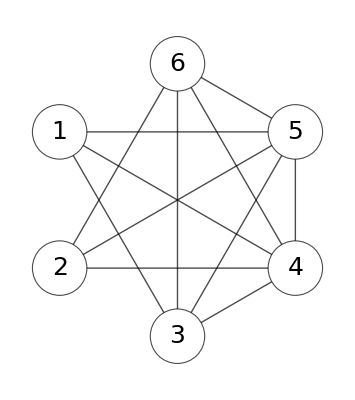

```mathematica
MYgraffon = Graph[vertex,edges, VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"CircularEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]
```

## Task 3

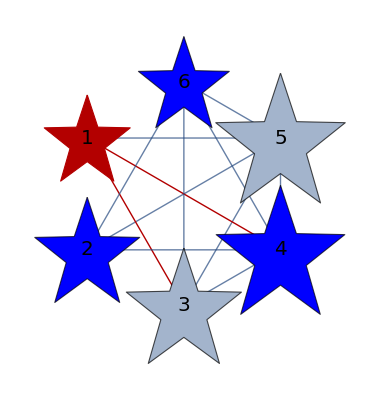
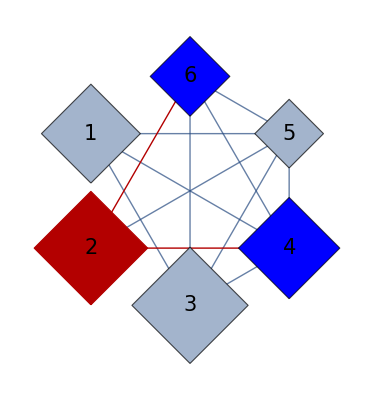
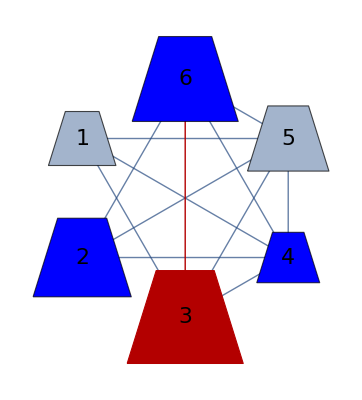
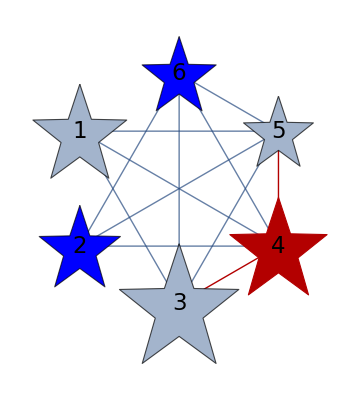
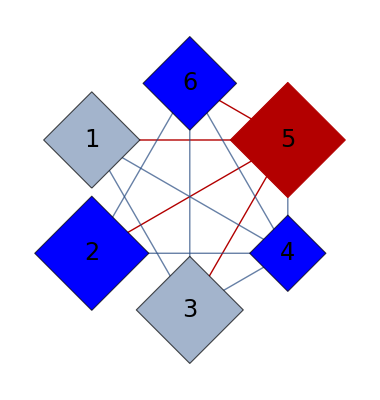
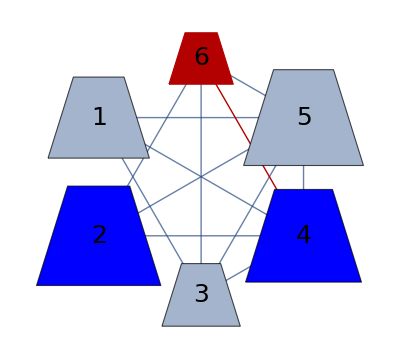

```mathematica
Table[Graph[vertex,edges, VertexSize->Table[i->RandomReal[{0.5,1}],{i,1,6}],VertexShapeFunction-> {"UpTrapezoid", "Star", "Diamond"}⟦Mod[k,3]+1⟧,VertexStyle->{_?EvenQ->Blue}, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,19+k],GraphHighlight->{k,_->k}, GraphLayout->{"CircularEmbedding"}],{k,1,6}]
```

## Task 4

```mathematica
getMyGraph[vertexNum_,edgesNum_]:=(
ClearAll[edges,vertex];
vertex = Table[i,{i,1,vertexNum}];
edges = Table[i->#&/@RandomChoice[vertex,edgesNum],{i,1,vertexNum}];
edges = RandomChoice[Flatten[edges],edgesNum];
Graph[vertex,edges]
)
```

```mathematica
getMyGraph[6,15]
```

-Graphics-

## Task 5

```mathematica
edges1 = DeleteDuplicates[RandomChoice[edges, RandomInteger[{1, Length[edges]}]]]
```

{5->2,3->4,2->3,2->6,4->5,2->1,6->2,5->1}

```mathematica
edges2 = DeleteDuplicates[RandomChoice[edges, RandomInteger[{1, Length[edges]}]]]
```

{5->1,4->3,3->6,6->2,4->5,5->2}

```mathematica
GetSortedList = Intersection[edges1,edges2]
```

{4->5,5->1,5->2,6->2}

```mathematica
positions1 = Flatten[Table[Position[edges1,GetSortedList⟦i⟧],{i,1, Length[GetSortedList]}]]
```

{5,8,1,7}

```mathematica
positions2 = Flatten[Table[Position[edges2,GetSortedList⟦i⟧],{i,1, Length[GetSortedList]}]]
```

{5,1,6,4}

```mathematica
edges1 = Flatten[Table[Property[edges1⟦i⟧,EdgeStyle->Green],{i,Length[edges1]}]];
```

```mathematica
Table[edges1⟦positions1⟦i⟧⟧ = Property[edges1⟦positions1⟦i⟧,1⟧,EdgeStyle->Yellow],{i,Length[positions1]}];
```

```mathematica
edges2 = Flatten[Table[Property[edges2⟦i⟧,EdgeStyle->Blue],{i,Length[edges2]}]];
```

```mathematica
Table[edges2⟦positions2⟦i⟧⟧ = Property[edges2⟦positions2⟦i⟧,1⟧,EdgeStyle->Pink],{i,Length[positions2]}];
```

```mathematica
edges = edges1~Join~edges2
```

{Property[5->2,EdgeStyle→RGBColor[1, 1, 0]],Property[3->4,EdgeStyle→RGBColor[0, 1, 0]],Property[2->3,EdgeStyle→RGBColor[0, 1, 0]],Property[2->6,EdgeStyle→RGBColor[0, 1, 0]],Property[4->5,EdgeStyle→RGBColor[1, 1, 0]],Property[2->1,EdgeStyle→RGBColor[0, 1, 0]],Property[6->2,EdgeStyle→RGBColor[1, 1, 0]],Property[5->1,EdgeStyle→RGBColor[1, 1, 0]],Property[5->1,EdgeStyle→RGBColor[1, 0.5, 0.5]],Property[4->3,EdgeStyle→RGBColor[0, 0, 1]],Property[3->6,EdgeStyle→RGBColor[0, 0, 1]],Property[6->2,EdgeStyle→RGBColor[1, 0.5, 0.5]],Property[4->5,EdgeStyle→RGBColor[1, 0.5, 0.5]],Property[5->2,EdgeStyle→RGBColor[1, 0.5, 0.5]]}

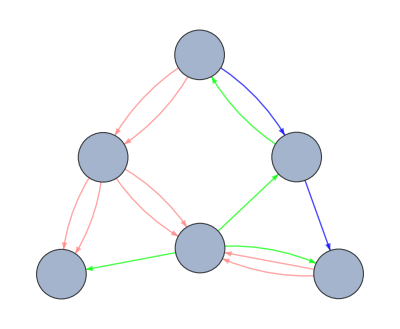

```mathematica
Graph[vertex,edges,VertexLabels->Placed["Name",Center],VertexSize->Large]
```